```mathematica
FindRoot[10*x^2*(1-x)^3-0.1==0,{x,0.7}]
```

{x→0.735618}

```mathematica
FindRoot[10*x^2*(1-x)^3-0.1==0,{x,0.2}]
```

{x→0.121433}

```mathematica
%%%%%%%%interior,u=2
```

```mathematica
FindRoot[10*(2/3)^2*(1-2/3)^3*y-0.1==0,{y,0.7}]
```

{y→0.6075}

```mathematica
%%%%%%%interior,u=2/3
```

```mathematica
FindRoot[10*(0.4)^2*(1-0.4)^3*y-0.1==0,{y,0.7}]
```

{y→0.289352}

```mathematica
%%%%%%%%u=0.5
```

```mathematica
FindRoot[10*(1/3)^2*(1-1/3)^3*y-0.1==0,{y,0.7}]
```

{y→0.30375}

```mathematica
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
```

```mathematica
Show[Show[VectorPlot[{x*(1-x) *((((N-1)!)/((M-1)!*(N-M)!))*y-0.1),y*(1-y)*1/(1+exp(beta*(x-T)))},{x,0,1},{x,0,1},VectorColorFunction->"Rainbow",VectorScale->{Automatic,Automatic,None},PlotLabel->Style["(a)",36],Axes->None,Frame->True,FrameLabel->{"Fraction of rich cooperators","Fraction of poor cooperators"},LabelStyle->Directive[Black,20]],ListPlot[{{0,0},{0.7,0}},PlotStyle->{PointSize[0.04],Black}]],Graphics[{Thick,Circle[{0.0758490766813128,0},{0.015,0.0065}],Circle[{0,0.16},{0.015,0.0065}],Circle[{0.4773906688921047,0.3},{0.015,0.0065}],Circle[{0.7,0},{0.015,0.0065}],Circle[{0.7,0.3},{0.015,0.0065}],Circle[{0,0.3},{0.015,0.0065}]}]]
```

```mathematica
%%%%%%%%%%%%%%%%%u=2
```

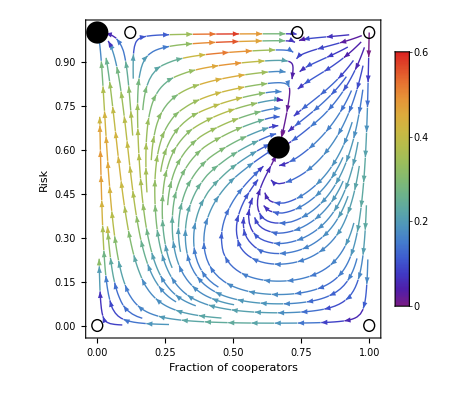

```mathematica
Show[Show[StreamPlot[{1/0.1*x*(1-x) *((((6-1)!)/((3-1)!*(6-3)!))*x^2*(1-x)^3*y-0.1),y*(1-y)*(2*(1-x)-x)},{x,0,1},{y,0,1},PlotLegends->Automatic,StreamColorFunction->"Rainbow",StreamScale->{Automatic,Automatic,None},Axes->None,Frame->True,FrameLabel->{"Fraction of cooperators","Risk"},LabelStyle->Directive[Black,20]],ListPlot[{{0,1},{2/3,0.6075}},PlotStyle->{PointSize[0.04],Black}]],Graphics[{Thick,Circle[{0,0},{0.02,0.02}],Circle[{1,0},{0.02,0.02}],Circle[{1,1},{0.02,0.02}],Circle[{0.7356180923175425,1},{0.02,0.02}],Circle[{0.12143333357849782,1},{0.02,0.02}]}]]
```

```mathematica
%%%%%%%%%%%%%%%%%u=2/3
```

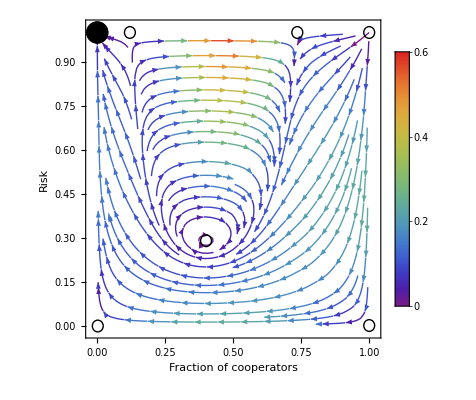

```mathematica
Show[Show[StreamPlot[{1/0.1*x*(1-x) *((((6-1)!)/((3-1)!*(6-3)!))*x^2*(1-x)^3*y-0.1),y*(1-y)*(2/3*(1-x)-x)},{x,0,1},{y,0,1},PlotLegends->Automatic,StreamColorFunction->"Rainbow",StreamScale->{Automatic,Automatic,None},Axes->None,Frame->True,FrameLabel->{"Fraction of cooperators","Risk"},LabelStyle->Directive[Black,20]],ListPlot[{{0,1}},PlotStyle->{PointSize[0.04],Black}]],Graphics[{Thick,Circle[{0,0},{0.02,0.02}],Circle[{1,0},{0.02,0.02}],Circle[{1,1},{0.02,0.02}],Circle[{0.40,0.28935185185185186},{0.02,0.02}],Circle[{0.7356180923175425,1},{0.02,0.02}],Circle[{0.12,1},{0.02,0.02}]}]]
```

```mathematica
%%%%%%%%%%%%%%%%%%%u=0.5
```

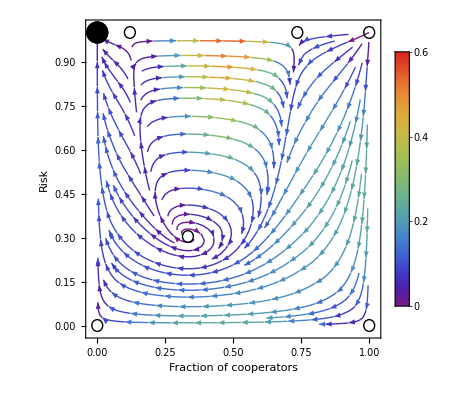

```mathematica
Show[Show[StreamPlot[{1/0.1*x*(1-x) *((((6-1)!)/((3-1)!*(6-3)!))*x^2*(1-x)^3*y-0.1),y*(1-y)*(0.5*(1-x)-x)},{x,0,1},{y,0,1},PlotLegends->Automatic,StreamColorFunction->"Rainbow",StreamScale->{Automatic,Automatic,None},Axes->None,Frame->True,FrameLabel->{"Fraction of cooperators","Risk"},LabelStyle->Directive[Black,20]],ListPlot[{{0,1}},PlotStyle->{PointSize[0.04],Black}]],Graphics[{Thick,Circle[{0,0},{0.02,0.02}],Circle[{1,0},{0.02,0.02}],Circle[{1,1},{0.02,0.02}],Circle[{1/3,0.30375},{0.02,0.02}],Circle[{0.7356180923175425,1},{0.02,0.02}],Circle[{0.12,1},{0.02,0.02}]}]]
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%%%%%%%%u=4
```

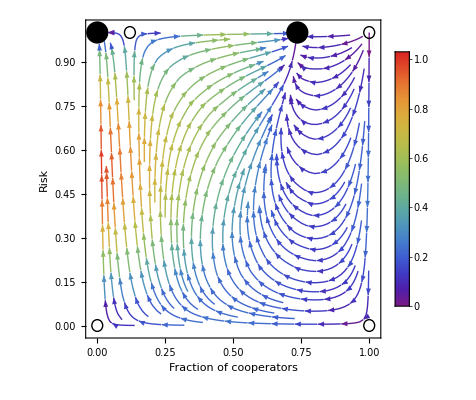

```mathematica
Show[Show[StreamPlot[{1/0.1*x*(1-x) *((((6-1)!)/((3-1)!*(6-3)!))*x^2*(1-x)^3*y-0.1),y*(1-y)*(4*(1-x)-x)},{x,0,1},{y,0,1},PlotLegends->Automatic,StreamColorFunction->"Rainbow",StreamScale->{Automatic,Automatic,None},Axes->None,Frame->True,FrameLabel->{"Fraction of cooperators","Risk"},LabelStyle->Directive[Black,20]],ListPlot[{{0,1},{0.7356180923175425,1}},PlotStyle->{PointSize[0.04],Black}]],Graphics[{Thick,Circle[{0,0},{0.02,0.02}],Circle[{1,0},{0.02,0.02}],Circle[{1,1},{0.02,0.02}],Circle[{0.12,1},{0.02,0.02}]}]]
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%exponential feedbacks
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%interior, T=0.5
```

```mathematica
FindRoot[10*(0.5)^2*(1-0.5)^3*y-0.1==0,{y,0.7}]
```

{y→0.32}

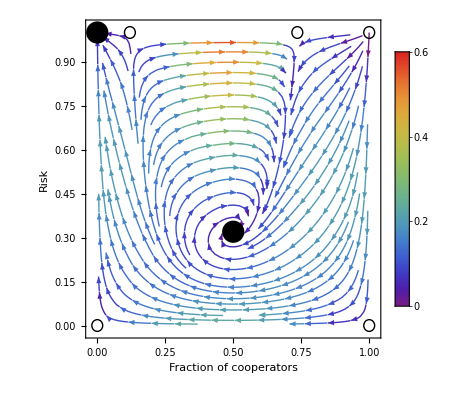

```mathematica
Show[Show[StreamPlot[{1/0.1*x*(1-x) *((((6-1)!)/((3-1)!*(6-3)!))*x^2*(1-x)^3*y-0.1),y*(1-y)*(1/(1+E^(5*(x-0.5)))-1/(1+E^(-5*(x-0.5))))},{x,0,1},{y,0,1},PlotLegends->Automatic,StreamColorFunction->"Rainbow",StreamScale->{Automatic,Automatic,None},Axes->None,Frame->True,FrameLabel->{"Fraction of cooperators","Risk"},LabelStyle->Directive[Black,20]],ListPlot[{{0,1},{0.5,0.32}},PlotStyle->{PointSize[0.04],Black}]],Graphics[{Thick,Circle[{0,0},{0.02,0.02}],Circle[{1,0},{0.02,0.02}],Circle[{1,1},{0.02,0.02}],Circle[{0.7356180923175425,1},{0.02,0.02}],Circle[{0.12,1},{0.02,0.02}]}]]
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%interior, T=0.4
```

```mathematica
FindRoot[10*(0.4)^2*(1-0.4)^3*y-0.1==0,{y,0.7}]
```

{y→0.289352}

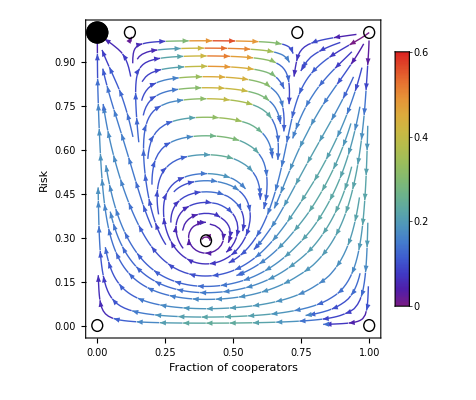

```mathematica
Show[Show[StreamPlot[{1/0.1*x*(1-x) *((((6-1)!)/((3-1)!*(6-3)!))*x^2*(1-x)^3*y-0.1),y*(1-y)*(1/(1+E^(5*(x-0.4)))-1/(1+E^(-5*(x-0.4))))},{x,0,1},{y,0,1},PlotLegends->Automatic,StreamColorFunction->"Rainbow",StreamScale->{Automatic,Automatic,None},Axes->None,Frame->True,FrameLabel->{"Fraction of cooperators","Risk"},LabelStyle->Directive[Black,20]],ListPlot[{{0,1}},PlotStyle->{PointSize[0.04],Black}]],Graphics[{Thick,Circle[{0,0},{0.02,0.02}],Circle[{1,0},{0.02,0.02}],Circle[{1,1},{0.02,0.02}],Circle[{0.4,0.28935185185185186},{0.02,0.02}],Circle[{0.7356180923175425,1},{0.02,0.02}],Circle[{0.12,1},{0.02,0.02}]}]]
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%interior, T=0.2
```

```mathematica
FindRoot[10*(0.2)^2*(1-0.2)^3*y-0.1==0,{y,0.7}]
```

{y→0.488281}

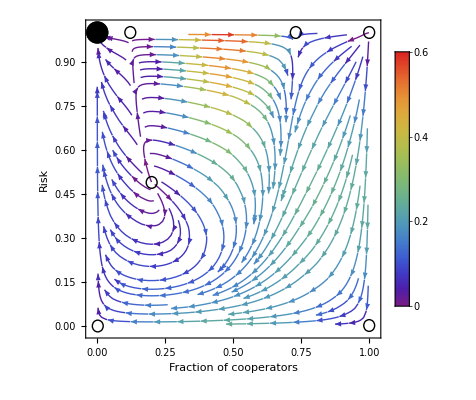

```mathematica
Show[Show[StreamPlot[{1/0.1*x*(1-x) *((((6-1)!)/((3-1)!*(6-3)!))*x^2*(1-x)^3*y-0.1),y*(1-y)*(1/(1+E^(5*(x-0.2)))-1/(1+E^(-5*(x-0.2))))},{x,0,1},{y,0,1},PlotLegends->Automatic,StreamColorFunction->"Rainbow",StreamScale->{Automatic,Automatic,None},Axes->None,Frame->True,FrameLabel->{"Fraction of cooperators","Risk"},LabelStyle->Directive[Black,20]],ListPlot[{{0,1}},PlotStyle->{PointSize[0.04],Black}]],Graphics[{Thick,Circle[{0,0},{0.02,0.02}],Circle[{1,0},{0.02,0.02}],Circle[{0.2,0.4882812499999999},{0.02,0.02}],Circle[{1,1},{0.02,0.02}],Circle[{0.73,1},{0.02,0.02}],Circle[{0.12143333357849782,1},{0.02,0.02}]}]]
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%T=0.8
```

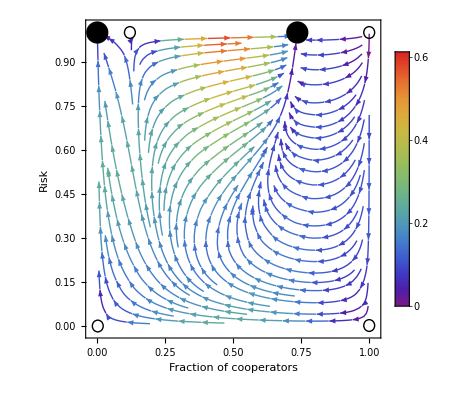

```mathematica
Show[Show[StreamPlot[{1/0.1*x*(1-x) *((((6-1)!)/((3-1)!*(6-3)!))*x^2*(1-x)^3*y-0.1),y*(1-y)*(1/(1+E^(5*(x-0.8)))-1/(1+E^(-5*(x-0.8))))},{x,0,1},{y,0,1},PlotLegends->Automatic,StreamColorFunction->"Rainbow",StreamScale->{Automatic,Automatic,None},Axes->None,Frame->True,FrameLabel->{"Fraction of cooperators","Risk"},LabelStyle->Directive[Black,20]],ListPlot[{{0,1},{0.7356180923175425,1}},PlotStyle->{PointSize[0.04],Black}]],Graphics[{Thick,Circle[{0,0},{0.02,0.02}],Circle[{1,0},{0.02,0.02}],Circle[{1,1},{0.02,0.02}],Circle[{0.12,1},{0.02,0.02}]}]]
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
```